```mathematica
Solve[{ax + by == 1, x-y ==2}, {x,y}]
```

Solve::ivar: π/3 is not a valid variable.

```mathematica
Solve[{ax+by==1,π/3-y==2},{π/3,y}]
clear
```

Solve::ivar: π/3 is not a valid variable.

Solve[{ax+by==1,π/3-y==2},{π/3,y}]

clear

```mathematica
cls
```

cls

```mathematica
x
```

π/3

```mathematica
Solve[{a u + b v == 1, u - v ==2}, {u,v}][
```

```mathematica
{{u->-(-1-2 b)/(2 b),v->-(-1+2 b)/(2 b)}}
Solve[list[a u + b v == 1, u - v ==2],{u,v}]
```

{{u→-(-1-2 b)/(2 b),v→-(-1+2 b)/(2 b)}}

Solve::naqs: list[b u+b v==1,u-v==2] is not a quantified system of equations and inequalities.

Solve[list[b u+b v==1,u-v==2],{u,v}]

```mathematica
fF[g_] = Piecewise[{{g/2, 0<= g <=1.5}, {1, 1.5 < g <= 2}}]
```

Piecewise[{{g/2, 0≤g≤1.5}, {1, 1.5<g≤2}, {0, True}}]

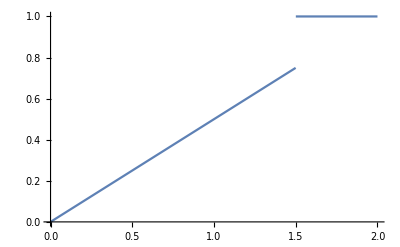

```mathematica
Piecewise[{{g/2, 0≤g≤1.5}, {1, 1.5<g≤2}, {0, True}}]
Plot[fF[g], {g,0,2}]
```

```mathematica
F[t_] = FourierSinSeries[fF[t], t, 5]
```

0.593698 Sin[t]+0.14051 Sin[2 t]-0.249511 Sin[3 t]+0.0558022 Sin[4 t]+0.129811 Sin[5 t]

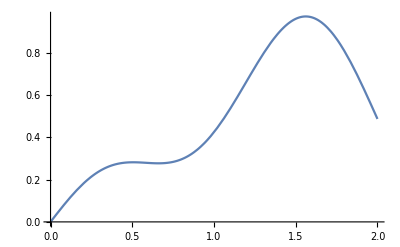

```mathematica
Plot[%, {t, 0, 2}]
```

```mathematica
F[t_] = FourierSinSeries[fF[t], t, 100]
```

0.593698 Sin[t]+0.14051 Sin[2 t]-0.249511 Sin[3 t]+0.0558022 Sin[4 t]+0.129811 Sin[5 t]-0.11006 Sin[6 t]-0.0289623 Sin[7 t]+0.0903274 Sin[8 t]-0.0330287 Sin[9 t]-0.0360002 Sin[10 t]+0.0458371 Sin[11 t]-0.0154057 Sin[12 t]-0.0207967 Sin[13 t]+0.0389045 Sin[14 t]-0.0165019 Sin[15 t]-0.0300993 Sin[16 t]+0.0409107 Sin[17 t]+0.0028823 Sin[18 t]-0.0403625 Sin[19 t]+0.0216705 Sin[20 t]+0.0197383 Sin[21 t]-0.0283712 Sin[22 t]+0.00508856 Sin[23 t]+0.0155837 Sin[24 t]-0.018433 Sin[25 t]+0.00607693 Sin[26 t]+0.014144 Sin[27 t]-0.0220448 Sin[28 t]+0.00207024 Sin[29 t]+0.0232987 Sin[30 t]-0.0178046 Sin[31 t]-0.0112184 Sin[32 t]+0.0225597 Sin[33 t]-0.00458269 Sin[34 t]-0.0141162 Sin[35 t]+0.0133011 Sin[36 t]-0.00101083 Sin[37 t]-0.0099451 Sin[38 t]+0.012681 Sin[39 t]-0.0020933 Sin[40 t]-0.0140112 Sin[41 t]+0.0140737 Sin[42 t]+0.00549228 Sin[43 t]-0.0180798 Sin[44 t]+0.00602549 Sin[45 t]+0.0120895 Sin[46 t]-0.0123641 Sin[47 t]-0.00077904 Sin[48 t]+0.00947426 Sin[49 t]-0.00809473 Sin[50 t]+0.000251684 Sin[51 t]+0.00902726 Sin[52 t]-0.0100605 Sin[53 t]-0.0022066 Sin[54 t]+0.0136175 Sin[55 t]-0.00704179 Sin[56 t]-0.00915705 Sin[57 t]+0.0121501 Sin[58 t]+0.000325967 Sin[59 t]-0.00974823 Sin[60 t]+0.00660372 Sin[61 t]+0.00168895 Sin[62 t]-0.00707268 Sin[63 t]+0.00652011 Sin[64 t]+0.00115542 Sin[65 t]-0.00960914 Sin[66 t]+0.00677932 Sin[67 t]+0.00604096 Sin[68 t]-0.0112441 Sin[69 t]+0.00118813 Sin[70 t]+0.00936637 Sin[71 t]-0.00681567 Sin[72 t]-0.00266359 Sin[73 t]+0.00696452 Sin[74 t]-0.00421265 Sin[75 t]-0.00166694 Sin[76 t]+0.00676021 Sin[77 t]-0.00536309 Sin[78 t]-0.00363615 Sin[79 t]+0.00941245 Sin[80 t]-0.00260626 Sin[81 t]-0.00798548 Sin[82 t]+0.00743167 Sin[83 t]+0.0023729 Sin[84 t]-0.00747403 Sin[85 t]+0.00339888 Sin[86 t]+0.0027511 Sin[87 t]-0.00540797 Sin[88 t]+0.00350125 Sin[89 t]+0.00247524 Sin[90 t]-0.007154 Sin[91 t]+0.00316447 Sin[92 t]+0.00600819 Sin[93 t]-0.00752228 Sin[94 t]-0.00119353 Sin[95 t]+0.00762696 Sin[96 t]-0.00373861 Sin[97 t]-0.00349259 Sin[98 t]+0.00531896 Sin[99 t]-0.0020114 Sin[100 t]

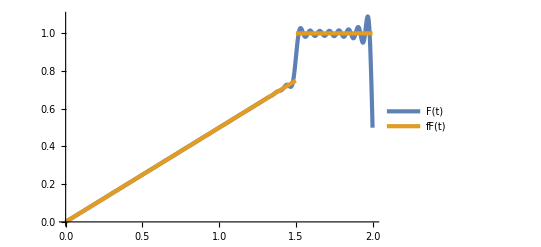

```mathematica
Plot[{F[t], fF[t]}, {t,0,2}, {PlotLegends->"Expressions", PlotTheme->"ThickLines"}]
```